```mathematica
SetDirectory["C:/Users/serha/OneDrive/Masaüstü/MyRepo/master_thesis_MMT003/210224_impacts_in_time_windows"];
```

```mathematica
(*data=Import["data_with_time_windows2.mx"];*)
```

```mathematica
datafullmodified=Import["datafull_manipulated.mx"];
```

```mathematica
data=Table[Take[datafullmodified,UpTo@i],{i,{46497,91690,138440,183584,230005,275844,320350,367179,413106,459203}}];
```

```mathematica
Get["../algoritm_packages/SingleNetworks-algorithm-package.wl"]
(* ?SingleNetworks`* *)
```

Thickness Feature

```mathematica
window=10;
rawaim=data[[window]][[All,10]];
pos=Partition[Flatten@Table[Position[rawaim,i],{i,{"NA",0}}],1];
```

```mathematica
aim=Delete[rawaim,pos];
```

```mathematica
campaign=Delete[data[[window]][[All,2]],pos];
```

```mathematica
seri=Delete[data[[window]][[All,1]],pos];
```

```mathematica
Print["unique aim data members: ",Dimensions@DeleteDuplicates@aim]
Print["aim data length: ",Dimensions@aim]
Print["sequence data groups amount: ",Dimensions@DeleteDuplicates@campaign]
```

unique aim data members: {35}

aim data length: {396124}

sequence data groups amount: {675}

```mathematica
Print["bucket size: ",bucketsize=Floor@(N@(Dimensions@aim)/50)]
aimlabeled=Thread[Range@Length@aim->aim];
aimpartitioned=Partition[Normal@Sort@Association@aimlabeled,UpTo@bucketsize];
bins=Table[MinMax[i],{i,Values@aimpartitioned}];
Print["node amount: ",Length@bins];
```

bucket size: {7922}

node amount: 51

```mathematica
Tally@bins
```

{{{41,56},1},{{56,56},1},{{56,57},1},{{57,63},1},{{63,65},1},{{65,65},25},{{65,66},1},{{66,66},2},{{66,67},1},{{67,67},12},{{67,74},1},{{74,76},1},{{76,77},1},{{77,87},1},{{87,87},1}}

```mathematica
repetitivesreport=DeleteCases[Tally@bins,x_/;x[[2]]==1];
repetitives=repetitivesreport[[All,1]];
labelgeneration[x_]:=Table[{repetitives[[x]][[1]]+i*repetitives[[x]][[1]]/10^(RealDigits@repetitives[[x]][[1]])[[2]],repetitives[[x]][[2]]+i*repetitives[[x]][[2]]/10^(RealDigits@repetitives[[x]][[2]])[[2]]},{i,Range@repetitivesreport[[x]][[2]]}]
binsrearranged=ReplacePart[bins,Flatten[Table[MapThread[#1->#2&,{Flatten@Position[bins,repetitives[[g]]],labelgeneration[g]}],{g,Range@Length@repetitives}],1]];
```

```mathematica
aimbinned=Values@Normal@KeySort@Association@Flatten[Table[aimpartitioned[[i]]/.Table[Values@aimpartitioned[[i]][[j]]->binsrearranged[[i]],{j,Length@aimpartitioned[[i]]}],{i,Length@aimpartitioned}],1];
Position[aimbinned,Null]
```

{}

```mathematica
aim=aimbinned;
binningmembers=Sort[DeleteDuplicates[aim]];
Print["binning amount: ",Dimensions@DeleteDuplicates@aimbinned]
Print["dimension of binned data: ",Dimensions@aim]
Print["binning members dimension : ",Dimensions@binningmembers]
```

binning amount: {51,2}

dimension of binned data: {396122,2}

binning members dimension : {51,2}

```mathematica
binningmembers=Sort[N@DeleteDuplicates[aim]]
```

{{41.,56.},{56.,56.},{56.,57.},{57.,63.},{63.,65.},{65.,66.},{65.65,65.65},{66.,67.},{66.3,66.3},{66.66,66.66},{66.95,66.95},{67.,74.},{67.32,67.32},{67.6,67.6},{67.67,67.67},{68.25,68.25},{68.34,68.34},{68.9,68.9},{69.01,69.01},{69.55,69.55},{69.68,69.68},{70.2,70.2},{70.35,70.35},{70.85,70.85},{71.02,71.02},{71.5,71.5},{71.69,71.69},{72.15,72.15},{72.36,72.36},{72.8,72.8},{73.03,73.03},{73.45,73.45},{73.7,73.7},{74.,76.},{74.1,74.1},{74.37,74.37},{74.75,74.75},{75.04,75.04},{75.4,75.4},{76.,77.},{76.05,76.05},{76.7,76.7},{77.,87.},{77.35,77.35},{78.,78.},{78.65,78.65},{79.3,79.3},{79.95,79.95},{80.6,80.6},{81.25,81.25},{87.,87.}}

```mathematica
aimbaskets=Values@GroupBy[Thread[{aim,campaign}],Last->First];
aimbasketsrev=Table[DeleteDuplicates[i],{i,aimbaskets}];
Print["binning groups association to count of their total members: ",KeySort@Counts@aim]
Print["binning amount: ",Dimensions@DeleteDuplicates@aim]
```

Thread::tdlen: Objects of unequal length in {<<2>>} cannot be combined.

binning groups association to count of their total members: <|{41,56}→7922,{56,56}→7922,{56,57}→7922,{57,63}→7922,{63,65}→7920,{65,66}→7922,{1313/20,1313/20}→7922,{66,67}→7922,{663/10,663/10}→7922,{3333/50,3333/50}→7922,{1339/20,1339/20}→7922,{67,74}→7922,{1683/25,1683/25}→7922,{338/5,338/5}→7922,{6767/100,6767/100}→7922,{273/4,273/4}→7922,{3417/50,3417/50}→7922,{689/10,689/10}→7922,{6901/100,6901/100}→7922,{1391/20,1391/20}→7922,{1742/25,1742/25}→7922,{351/5,351/5}→7922,{1407/20,1407/20}→7922,{1417/20,1417/20}→7922,{3551/50,3551/50}→7922,{143/2,143/2}→7922,{7169/100,7169/100}→7922,{1443/20,1443/20}→7922,{1809/25,1809/25}→7922,{364/5,364/5}→7922,{7303/100,7303/100}→7922,{1469/20,1469/20}→7922,{737/10,737/10}→7922,{74,76}→7922,{741/10,741/10}→7922,{7437/100,7437/100}→7922,{299/4,299/4}→7922,{1876/25,1876/25}→7922,{377/5,377/5}→7922,{76,77}→7922,{1521/20,1521/20}→7922,{767/10,767/10}→7922,{77,87}→7922,{1547/20,1547/20}→7922,{78,78}→7922,{1573/20,1573/20}→7922,{793/10,793/10}→7922,{1599/20,1599/20}→7922,{403/5,403/5}→7922,{325/4,325/4}→7922,{87,87}→24|>

binning amount: {51,2}

```mathematica
AbsoluteTiming[singlesupportvalues=Table[N[Count[Table[MemberQ[i,j],{i,aimbasketsrev}],True]/Length[aimbasketsrev]],{j,binningmembers}];]
pairs=Subsets[binningmembers,{2}];
Dimensions[binningmembers]
Dimensions[pairs]
Dimensions[aimbasketsrev]
AbsoluteTiming[pairsupportvalues=Table[N[Count[Table[SubsetQ[i,j],{i,aimbasketsrev}],True]/
Length[aimbasketsrev]],{j,pairs}];]
```

{0.0002111,Null}

{51,2}

{1275,2,2}

{2,1}

{0.0228519,Null}

```mathematica
AbsoluteTiming[liftvalues=pairsupportvalues/(DeleteCases[Flatten@UpperTriangularize[Table[singlesupportvalues[[j]]*singlesupportvalues[[k]],{j,Length[binningmembers]},{k,Length[binningmembers]}],1],0.]);]
```

Thread::tdlen: Objects of unequal length in {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,«1265»} {} cannot be combined.

{0.0044224,Null}

```mathematica
allmatrixelements=Sort[Join[pairs,Reverse[pairs,2],Table[{i,i},{i,binningmembers}]]];
```

{0}

{0.0050556,Null}

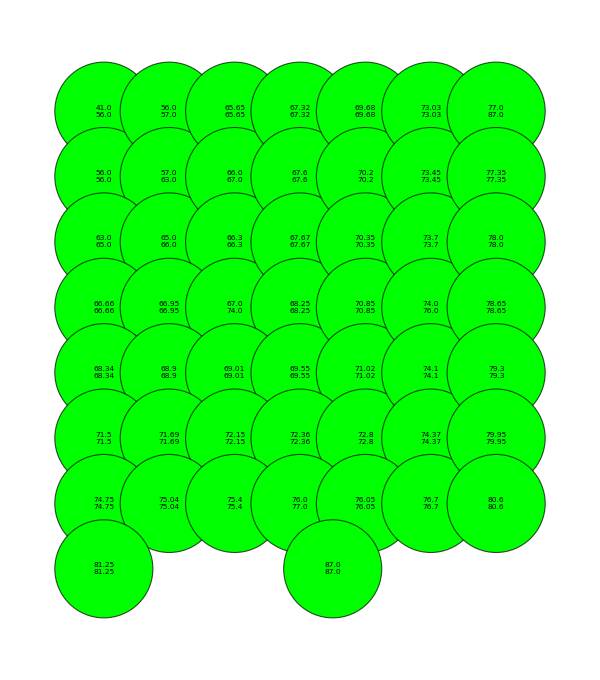

```mathematica
likelypairs=Extract[pairs,Position[liftvalues,x_/;x>1]];
Dimensions@likelypairs
AbsoluteTiming[binarymatrix=ArrayReshape[Table[If[j==True,1,0],{j,Table[MemberQ[likelypairs,i],{i,allmatrixelements}]}],{Length@binningmembers,Length@binningmembers}];]
graph=AdjacencyGraph[binarymatrix,{GraphLayout->Automatic,DirectedEdges->False,EdgeShapeFunction->"Line",VertexSize->1.5,VertexStyle->Green,VertexLabelStyle->Directive[Black,Italic,7.5],VertexLabels->Flatten[MapThread[{#1->Placed[#2,Center]}&,{Range[1,Dimensions[binarymatrix][[1]]],
Table[StringRiffle[i,"\n"],{i,binningmembers}]}]]},ImageSize->600]
```